```mathematica
ClearAll["Global`*"]
```

```mathematica
a=150;b=100;
μ=0.025;μz=48;μG=4;
β=10;p=0.000004;
κ=8500000;A=370000;
α=1;αG=2;
u=0.351;
Iinit = 44;
```

```mathematica
(*Initial conditions at time of transfusion*)
Rinit=8500000;
Minit=0; (*Number of transfused cells that are infected x burst size*)
Pinit=0;
Ginit=0;
zinit=10000;
```

```mathematica
sol=NDSolve[{
R'[t]==A*(1-R[t]/κ)-μ*R[t]-p*R[t]*M[t],(*checked*)
M'[t]==Piecewise[{
{β*(1-u)*p*R[t-1]*M[t-1]*ⅇ^(-(μ))-μz*M[t]-p*R[t]*M[t],t>1},
{β*Iinit-μz*M[t]-p*R[t]*M[t],t≤ 1}}],
P'[t]==Piecewise[{
{(1-u)*p*R[t]*M[t]-μ*P[t]-a/(b+P[t])*P[t]-(1-u)*p*R[t-1]*M[t-1]*ⅇ^(-(μ)),t>1},
{(1-u)*p*R[t]*M[t]-μ*P[t]-a/(b+P[t])*P[t]-Iinit,t≤ 1}}],
G'[t]==u*p*R[t-2]*M[t-2]-μG*G[t],(*checked*)
G[t/;t≤0]==Ginit,R[t/;t≤0]==Rinit, M[t/;t≤ 0]==Minit,P[t/;t≤0]==Pinit},{R,M,P,G},{t,0,20}];
```

```mathematica
τ[t_]:=ⅇ^(-12.69+3.6*Log[G[t]])/(1+ⅇ^(-12.69+3.6*Log[G[t]]))
```

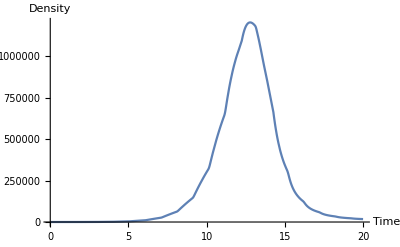

```mathematica
Plot[{P[t]/.sol},{t,0,20}, AxesLabel-> {"Time","Density"}]
```

```mathematica
RiemannSum[a_,b_,n_,t_]:=∑_(i=t)^n a/(b+(P[i]+P[i-1])/2)*(P[i]-P[i-1])
```

```mathematica
Rs[t_]:=a/(b+(P[t-α]+P[t-(2*α)/3])/2)*((t-(2*α)/3)-(t-(2*α)/3))+a/(b+(P[t-(2*α)/3]+P[t-α/3])/2)*((t-α/3)-(t-(2*α)/3))+a/(b+(P[t-α/3]+P[t])/2)*(t-(t-α/3));
R0[t_]:=a/(b+(P[0]+P[t/3])/2)*(t/3)+a/(b+(P[t/3]+P[(2*t)/3])/2)*(((2*t)/3)-(t/3))+a/(b+(P[(2*t)/3]+P[t])/2)*(t-((2*t)/3));
```

```mathematica
Rs[1]
```

-50/(100+1/2 (P[0]+P[1/3]))+(150 (2/3-i))/(100+1/2 (P[1/3]+P[2/3]))-50/(100+1/2 (P[2/3]+P[1]))